```mathematica
ode = {y''''[x]== 12 y'[x](y[x])^2 - 4, y'[-1]==0, y'[1]==0, y[-1]==-1, y[1]==1}
solution = NDSolve[ ode,y,{x, -1, 1}]
```

{y^(4)[x]==-4+12 y[x]^2 y'[x],y'[-1]==0,y'[1]==0,y[-1]==-1,y[1]==1}

{{y→InterpolatingFunction[{{-1., 1.}}, <>]}}

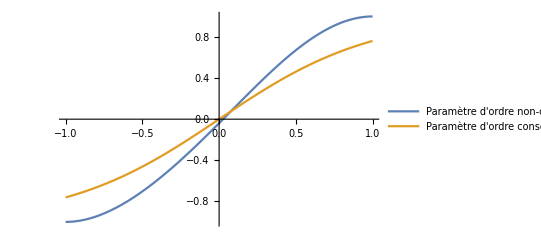

```mathematica
Plot[{y[x]/.solution, Tanh[x]},{x,-1,1},PlotLegends->{"Paramètre d'ordre non-conservé","Paramètre d'ordre conservé"}]
```

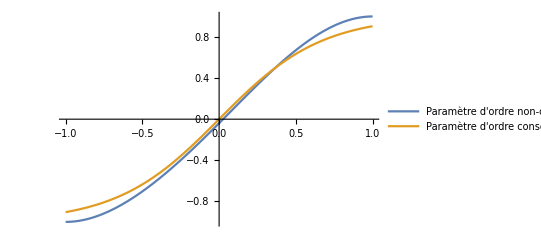

```mathematica
Plot[{y[x]/.solution, Tanh[1.5x]},{x,-1,1},PlotLegends->{"Paramètre d'ordre non-conservé","Paramètre d'ordre conservé"}]
```

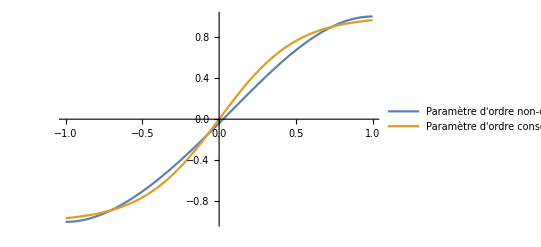

```mathematica
Plot[{y[x]/.solution, Tanh[2x]},{x,-1,1},PlotLegends->{"Paramètre d'ordre non-conservé","Paramètre d'ordre conservé"}]
```

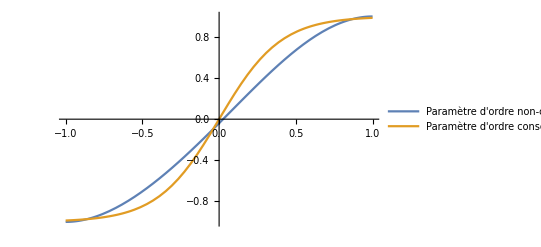

```mathematica
Plot[{y[x]/.solution, Tanh[2.5x]},{x,-1,1},PlotLegends->{"Paramètre d'ordre non-conservé","Paramètre d'ordre conservé"}]
```